```mathematica
(*Part (b)*)
```

```mathematica
F[η_,m_,z_]:=(1/Factorial[m-1])*Integrate[x^(m-1)/(z^(-1)*Exp[x]-η),{x,0,Infinity}]
```

```mathematica
D[F[η,5/2,z],z]/D[F[η,3/2,z],z]
```

PolyLog[3/2,z η]/PolyLog[1/2,z η]

```mathematica
F[η,3/2,z]/F[η,1/2,z]
```

PolyLog[3/2,z η]/PolyLog[1/2,z η]

```mathematica
(*Part (c)*)
```

```mathematica
f[η_,m_,z_]:=Sum[η^a*z^(a+1)/(a+1)^m,{a,0,5}]
```

```mathematica
dPdz=D[f[η,5/2,z]/(β*λ^3),z];
```

```mathematica
dndz=D[f[η,3/2,z]/(λ^3),z];
```

```mathematica
Series[dPdz/dndz,{z,0,3}]//FullSimplify
```

1/β-(η z)/(2 (√2 β))+((9-8 √3) η^2 z^2)/(36 β)+((14 √6-9 (3+√2)) η^3 z^3)/(72 β)+O[z]^4

```mathematica
(1/β)*Series[D[f[η,3/2,z]/f[η,1/2,z]],{z,0,3}]//FullSimplify
```

1/β-(η z)/(2 (√2 β))+((9-8 √3) η^2 z^2)/(36 β)+((14 √6-9 (3+√2)) η^3 z^3)/(72 β)+O[z]^4

```mathematica
Z=(n*λ^3)-η/2^(3/2)*(n*λ^3)^2+(1/4-1/3^(3/2))*(n*λ^3)^3;
```

```mathematica
ucPrime=Series[f[η,3/2,z]/f[η,1/2,z],{z,0,1}]//FullSimplify
```

1-(η z)/(2 √2)+O[z]^2

```mathematica
1-(η z)/(2 √2)/.{z->Z}//Expand
```

1-(n η λ^3)/(2 √2)+1/8 n^2 η^2 λ^6-(n^3 η λ^9)/(8 √2)+(n^3 η λ^9)/(6 √6)

```mathematica
Solve[EF==(hbar^2)/(2m)*(6*Pi^2*nMinus)^(2/3),nMinus]//FullSimplify
```

Solve::nongen: Solutions may not be valid for all values of parameters.

{{nMinus→(√2 ((EF m)/hbar^2)^(3/2))/(3 π^2)}}

```mathematica
kB*T/n*(1+(n λ^3)/(2 √2))//FullSimplify
```

(kB T (4+√2 n λ^3))/(4 n)

```mathematica
(kB T (4+√2 n λ^3))/(4 n)/.{n->Sqrt[2]*(m*EF/(hbar)^2)^(3/2)/(3*Pi^2)}//FullSimplify//Expand
```

(3 hbar^4 kB √((EF m)/hbar^2) π^2 T)/(√2 EF^2 m^2)+(kB T λ^3)/(2 √2)

```mathematica
Integrate[Integrate[e-e1-e2,{e2,0,e-e1}],{e1,0,e}]
```

e^3/6

```mathematica
Series[f[-1,d+1,z]/f[-1,d,z],{z,0,3}]
```

1+2^(-1-d) z+(-2^(-1-2 d)+2^(-2 d)+3^(-1-d)-3^-d) z^2-2^(-2-3 d) 3^(-1-d) (7 2^(1+2 d)-2 3^(1+d)-2^d 3^(2+d)) z^3+O[z]^4

```mathematica
Integrate[e^(d-1),{e,0,ef}]
```

ConditionalExpression[ef^d/d, Re[d]>0]

```mathematica
Series[(1+Pi^2/6*d*(d-1)*x)^(-1/d),{x,0,2}]//FullSimplify
```

1-1/6 ((-1+d) π^2) x+1/72 (-1+d)^2 (1+d) π^4 x^2+O[x]^3

```mathematica
Integrate[E^(-k*b*l*n),{n,0,Infinity}]
```

ConditionalExpression[1/(b k l), Re[b k l]>0]

```mathematica
Product[1/(1-E^(-b*l)),{l,0,Infinity}]
```

1/QPochhammer[1,ⅇ^-b]

```mathematica
Integrate[Log[1-E^(-b*l)],{l,0,Infinity}]
```

ConditionalExpression[-π^2/(6 b), Re[b]>0]

```mathematica
D[-π^2/(6 b),b]
```

π^2/(6 b^2)

```mathematica
D[-Pi^2/6*k^2*T^2,T]
```

-1/3 k^2 π^2 T

```mathematica
P=1/(4*e*Sqrt[3])*Exp[Pi*Sqrt[2*e/3]];
```

```mathematica
P*Log[P]//FullSimplify
```

-(ⅇ^(√(2/3) √e π) (Log[48]-2 Log[ⅇ^(√(2/3) √e π)/e]))/(8 √3 e)

```mathematica
Series[Log[1-Exp[-b*l]],{l,0,3}]
```

Log[b l]-(b l)/2+(b^2 l^2)/24+O[l]^4

```mathematica
Int=Integrate[Log[1-Exp[-b*l]],{l,0,Infinity}]
```

ConditionalExpression[-π^2/(6 b), Re[b]>0]

```mathematica
integral=Int-Integrate[Series[Log[1-Exp[-b*l]],{b,0,2}],{l,0,1}];
```

```mathematica
energy=D[integral,b]
```

ConditionalExpression[1/4-1/b-b/36+π^2/(6 b^2), Re[b]>0]

```mathematica
Solve[EE==π^2/(6 b^2)-1/b,b]//FullSimplify
```

{{b→-(3+√(9+6 EE π^2))/(6 EE)},{b→(-3+√(9+6 EE π^2))/(6 EE)}}

```mathematica
integralT=integral/.{b->(1/(kb*T))};
```

```mathematica
S=-D[kb*T*integralT,T]//Expand
```

ConditionalExpression[-2 kb-1/(72 kb T^2)+1/3 kb^2 π^2 T+kb Log[1/(kb T)], Re[1/(kb T)]>0]

```mathematica
Sβ=S/.{T->1/(kb*b)}
```

ConditionalExpression[-2 kb+(kb π^2)/(3 b)+kb Log[b], Re[b]>0]

```mathematica
D[Sβ,{b,2}]
```

ConditionalExpression[-kb/b^2+(2 kb π^2)/(3 b^3), Re[b]>0]

```mathematica
S''=D[Sβ,{b,2}]/.{b->1/(kb*T)}/.{T->Sqrt[6*e]/(kb*Pi)}
```

ConditionalExpression[-(6 e kb)/π^2+(4 √6 e^(3/2) kb)/π, √6 π Re[1/(√e)]>0]

```mathematica
newS=S/.{T->Sqrt[6*e]/(kb*Pi)}
```

ConditionalExpression[-2 kb+√(2/3) √e kb π+kb Log[π/(√6 √e)], √6 π Re[1/(√e)]>0]

```mathematica
Exp[(√(2/3) √e π+Log[π/(√6 √e)])]/Sqrt[2*Pi*(4 √6 e^(3/2))/π]//FullSimplify
```

(√(e^(3/2)) ⅇ^(√(2/3) √e π) π)/(4 2^(1/4) 3^(3/4) e^2)

```mathematica
Log[0]
```

-∞

```mathematica
Integrate[Exp[β*(-p^2/(2*m)-K*r^n)]*p^2*r^2,{p,0,Infinity},{r,0,Infinity}]
```

ConditionalExpression[(√(π/2) (K β)^(-3/n) Gamma[3/n])/(n (β/m)^(3/2)), Re[β/m]>0]

```mathematica
Integrate[e^n*Exp[-β*e],{e,0,Infinity}]
```

ConditionalExpression[β^(-1-n) Gamma[1+n], Re[n]>-1&&Re[β]>0]

```mathematica
(3 (2+n))/(2 n)//Expand
```

3/2+3/n

```mathematica
Solve[Exp[β*μ]==Exp[n*λ^2/2]-1,μ]
```

{{μ→ConditionalExpression[(2 ⅈ π C[1]+Log[-1+ⅇ^((n λ^2)/2)])/β, C[1]∈ℤ]}}

```mathematica
Limit[k*T*Log[Exp[m/T]-1],{T->0},Assumptions->{k>0},Direction->"FromAbove"]
```

ConditionalExpression[k m, m>0]

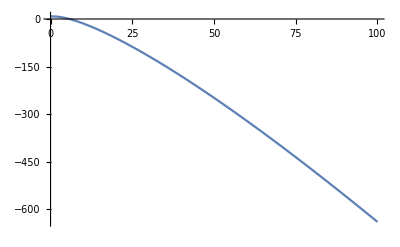

```mathematica
Plot[2*T*Log[Exp[4/T]-1],{T,0,100}]
```

```mathematica
Series[2*1/b*Log[Exp[b]-1],{b,0,3}]
```

(2 Log[b])/b+1+b/12-b^3/1440+O[b]^4